```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT,LEFT1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,1,0,m]],A:=Inverse[β[ω,δ,1,0,m]],T:=T[1,m]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,16000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[1,m].LEFT[ω,δ,t,ϵ,m].T[1,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[1,m].LEFT[ω,δ,t,ϵ,m].T[1,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,1,0,m].T[1,m].SR[ω,δ,1,0,m].T[1,m]].SL[ω,δ,1,0,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,1,0,m].T[1,m].SL[ω,δ,1,0,m].T[1,m]].SR[ω,δ,1,0,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,1,0,m].T[1,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].T[1,m].grr[ω,δ,t,ϵ,m].T[1,m]-T[1,m].GNON[ω,δ,t,ϵ,m].T[1,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[0,0.001,1,0,7]
```

6.99997

```mathematica
ρ[t_,m_]:=ρ[t,m] =t*IdentityMatrix[m]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,m_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ,m],T=ρ[1,m]},
sl1=Module[{J=SR[ω,δ,t,ϵ,m]},Do[J=Module[{c=RandomChoice[{gg,gg,Inverse[Module[{i=β[ω,δ,t,ϵ,m],μ1=RandomInteger[{1,m}]},ReplacePart[i,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},
Inverse[IdentityMatrix[m]-c.ConjugateTranspose[T].J.T].c],100]; J=J];Il1:=Inverse[IdentityMatrix[m]-sl1.ρ[1,m].SR[ω,δ,t,ϵ,m].ρ[1,m]].sl1;Ir1:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,t,ϵ,m];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].ρ[1,m].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]]];
η]
```

```mathematica
Timing[Mean[Table[tr1[1,0.001,1,0,1,7],2500]]]
```

{12.7942,1.52064}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,8],2500]]},{ω,Range[0,4,0.01]}]
```

```mathematica
{{0.,1.5411769044100336},{0.01,1.5795497688256257},{0.02,1.4783924741107637},{0.03,1.4306043772061443},{0.04,1.5346118551735912},{0.05,1.557363641133836},{0.06,1.7068135077995445},{0.07,1.9757888519203297},{0.08,2.2547590174614562},{0.09,2.703654757544479},{0.1,3.7328594336445837},{0.11,5.422729662219852},{0.12,11.616251992292863},{0.13,9.29438459203442},{0.14,6.474319159774119},{0.15,4.494291663905157},{0.16,3.203065134791699},{0.17,2.3586577424888464},{0.18,1.7839991682517873},{0.19,1.4924910962671278},{0.2,1.246094500105322},{0.21,1.141019553639005},{0.22,1.085976797051849},{0.23,1.0186670318301314},{0.24,1.0653183035543865},{0.25,1.0601284837342118},{0.26,1.0607362425998947},{0.27,1.0747071829408517},{0.28,1.085690550722543},{0.29,1.0922802802733014},{0.3,1.102364367371601},{0.31,1.1130696196544259},{0.32,1.0812998379163419},{0.33,1.052017577663071},{0.34,1.0547836442917724},{0.35000000000000003,1.0249942653110105},{0.36,0.9984010764941806},{0.37,0.9573325369050761},{0.38,0.9353990804458848},{0.39,0.9082051418230253},{0.4,0.8848927821672276},{0.41000000000000003,0.8787448103620178},{0.42,0.9359740657438109},{0.43,1.0511650257584233},{0.44,1.3989117874772625},{0.45,1.93679490541288},{0.46,3.4946963622575256},{0.47000000000000003,7.8632981665735135},{0.48,6.097895563947292},{0.49,4.424690109780891},{0.5,3.3251256555843125},{0.51,2.5359498677269743},{0.52,2.011462241266322},{0.53,1.6328670649887322},{0.54,1.3874490388817944},{0.55,1.321212183506952},{0.56,1.316599857411343},{0.5700000000000001,1.3206624594105003},{0.58,1.3838906371434487},{0.59,1.433891022031882},{0.6,1.4944975137834724},{0.61,1.5760367270846964},{0.62,1.5975789489465306},{0.63,1.6572208439068141},{0.64,1.6938158922876057},{0.65,1.7480907829721182},{0.66,1.7567261797506464},{0.67,1.7922609649263435},{0.68,1.8058585978917152},{0.6900000000000001,1.8161635135974545},{0.7000000000000001,1.8171201001728485},{0.71,1.840116620905167},{0.72,1.8416006375670662},{0.73,1.8571812073961629},{0.74,1.8546949927747296},{0.75,1.8407762471753988},{0.76,1.8439152084624104},{0.77,1.8199798251130266},{0.78,1.8032509757671273},{0.79,1.8093015635914123},{0.8,1.793736502412262},{0.81,1.8004377177788047},{0.8200000000000001,1.7675908291081626},{0.8300000000000001,1.7550890368654146},{0.84,1.7234236737506523},{0.85,1.6678737423259322},{0.86,1.612749289651999},{0.87,1.5804220739132504},{0.88,1.5417529527785403},{0.89,1.4855087653782597},{0.9,1.4135410550673797},{0.91,1.3339028047591956},{0.92,1.26487118859896},{0.93,1.1478738827777866},{0.9400000000000001,1.0621233707031021},{0.9500000000000001,0.9589242057736382},{0.96,0.8590175503413541},{0.97,0.8426656527501646},{0.98,1.0399164604021056},{0.99,1.7344458497141158},{1.,5.015146576598167},{1.01,4.663273766511844},{1.02,3.91366749819358},{1.03,2.97475458943961},{1.04,2.3300412260772756},{1.05,1.9088447084988696},{1.06,1.5713465490053535},{1.07,1.3513626738622664},{1.08,1.3253161155284703},{1.09,1.3558023998205668},{1.1,1.4094436103217536},{1.11,1.474052381568348},{1.12,1.534459841470054},{1.1300000000000001,1.6189125407778102},{1.1400000000000001,1.679571344326784},{1.1500000000000001,1.745514398356152},{1.16,1.8192760138112356},{1.17,1.839895767465388},{1.18,1.8791452780436058},{1.19,1.877839654791799},{1.2,1.9197640466647123},{1.21,1.9455192232130298},{1.22,1.985253625598255},{1.23,2.006205972315576},{1.24,2.010837259519042},{1.25,2.010309607608357},{1.26,2.035213174162821},{1.27,2.0484159200421077},{1.28,2.0313478542788843},{1.29,2.057894413565151},{1.3,2.0674663864989955},{1.31,2.053636308671211},{1.32,2.0485923931866563},{1.33,2.048782740359314},{1.34,2.061644641776624},{1.35,2.0457720248236706},{1.36,2.0505490369811388},{1.37,2.0209829009242593},{1.3800000000000001,2.022571380083031},{1.3900000000000001,2.0169402627681308},{1.4000000000000001,1.9958861807721837},{1.41,1.9871588203971904},{1.42,1.9836275020357717},{1.43,1.9462297668549684},{1.44,1.9337580050808298},{1.45,1.9130858073630097},{1.46,1.9024575925097194},{1.47,1.8722965289234308},{1.48,1.8508639196364636},{1.49,1.8424256486706905},{1.5,1.7982794213024917},{1.51,1.761488327818302},{1.52,1.7341317717914517},{1.53,1.684525264747136},{1.54,1.6371635740802848},{1.55,1.586232893235864},{1.56,1.4879878244488178},{1.57,1.4633432063398555},{1.58,1.3617787677057451},{1.59,1.2420968928806935},{1.6,1.1667843893859693},{1.61,0.994416300530271},{1.62,0.8779341732586933},{1.6300000000000001,0.7839011551110312},{1.6400000000000001,0.9764502203415308},{1.6500000000000001,2.276615123019006},{1.6600000000000001,3.63748285672074},{1.67,2.998444182435534},{1.68,2.4015442499395903},{1.69,1.9773920826637927},{1.7,1.6468665852190971},{1.71,1.4190731646075585},{1.72,1.2907510976115277},{1.73,1.1847514403891437},{1.74,1.245598640742204},{1.75,1.2496247510092893},{1.76,1.297685169436663},{1.77,1.4058388376630162},{1.78,1.4457431755639312},{1.79,1.5063380474572343},{1.8,1.5504833640950586},{1.81,1.6122775846863528},{1.82,1.6407526742306535},{1.83,1.6907971667884045},{1.84,1.7218195080367433},{1.85,1.744472829034767},{1.86,1.7665725350317618},{1.87,1.7729626965309253},{1.8800000000000001,1.8038506601537732},{1.8900000000000001,1.811156833584149},{1.9000000000000001,1.8169996543240614},{1.9100000000000001,1.8337260162689657},{1.92,1.8352837813214686},{1.93,1.8493732676500585},{1.94,1.8415389045182733},{1.95,1.8499157252965996},{1.96,1.8562760830334308},{1.97,1.8611103388093404},{1.98,1.8541036216848854},{1.99,1.8551299744304197},{2.,1.845914326284582},{2.0100000000000002,1.8539276656476942},{2.02,1.82997707943456},{2.0300000000000002,1.8359117651880725},{2.04,1.8406738603371795},{2.05,1.82564079639585},{2.06,1.8191101508984098},{2.07,1.8045072584252586},{2.08,1.8086074250577666},{2.09,1.7951823399204012},{2.1,1.7760889026346842},{2.11,1.7611754974260192},{2.12,1.7384600167407247},{2.13,1.7361794732857256},{2.14,1.7077520226357887},{2.15,1.6972676047231752},{2.16,1.6750293142174673},{2.17,1.6639088197537748},{2.18,1.6385954146645294},{2.19,1.60994960892593},{2.2,1.586720557549934},{2.21,1.5598008057097816},{2.22,1.52114481683015},{2.23,1.477188987292314},{2.24,1.442010996240477},{2.25,1.4058677188644078},{2.2600000000000002,1.3296474342263433},{2.27,1.2752677395916705},{2.2800000000000002,1.2010787016903588},{2.29,1.0971702580409686},{2.3000000000000003,1.0191339191274267},{2.31,0.914972201412777},{2.32,0.7531803417218258},{2.33,0.7236337745224986},{2.34,0.9822827501945821},{2.35,2.831014819582238},{2.36,2.785002071641402},{2.37,2.4776965460135556},{2.38,1.9839896675905278},{2.39,1.737065441416169},{2.4,1.437800806139741},{2.41,1.2003159006542725},{2.42,1.1374485956846603},{2.43,1.0291289454185266},{2.44,1.0196404424468735},{2.45,1.0489821717361967},{2.46,1.0679097328075684},{2.47,1.135342454107762},{2.48,1.1775425648397588},{2.49,1.240432127112404},{2.5,1.2806950681095812},{2.5100000000000002,1.3323721192823315},{2.52,1.3517362935957153},{2.5300000000000002,1.3920170808685117},{2.54,1.4093117315147057},{2.5500000000000003,1.4191869528405923},{2.56,1.4268284237125093},{2.57,1.4572706080596294},{2.58,1.4421392654558411},{2.59,1.4579893064958847},{2.6,1.4731524102895743},{2.61,1.467521456148367},{2.62,1.4787617130334518},{2.63,1.482094947822094},{2.64,1.475932895370357},{2.65,1.4695935848577584},{2.66,1.470096588145697},{2.67,1.4671481334534553},{2.68,1.4706193575528814},{2.69,1.4622752091025084},{2.7,1.4533542182101022},{2.71,1.4575848122280561},{2.72,1.4486131379331022},{2.73,1.4218162741952864},{2.74,1.4282283629647736},{2.75,1.4155816788331885},{2.7600000000000002,1.4025571090191822},{2.77,1.3990457816959647},{2.7800000000000002,1.3811807332687225},{2.79,1.3745835770688652},{2.8000000000000003,1.3517397744178132},{2.81,1.3548446023970293},{2.82,1.3352852871920475},{2.83,1.3170505235052565},{2.84,1.2945255401114115},{2.85,1.2756554080012932},{2.86,1.2551675427230358},{2.87,1.2323114863024676},{2.88,1.2050938123100094},{2.89,1.161637082852608},{2.9,1.14119886823498},{2.91,1.094508069573012},{2.92,1.048770532269447},{2.93,1.0067060372387178},{2.94,0.9463769904030968},{2.95,0.8799180245449039},{2.96,0.8007326540089921},{2.97,0.7038005613924765},{2.98,0.6226176091813943},{2.99,0.6527601084227999},{3.,1.6702687024870484},{3.0100000000000002,2.3397923524494293},{3.02,1.8912823642337437},{3.0300000000000002,1.681206532079698},{3.04,1.4944614575611195},{3.0500000000000003,1.3357672415630069},{3.06,1.0698685167008228},{3.0700000000000003,0.8988430524923464},{3.08,0.8084548904655284},{3.09,0.7379338948732124},{3.1,0.7120221063425796},{3.11,0.7458539567817928},{3.12,0.7414035944087606},{3.13,0.7981100058314184},{3.14,0.8294152135021191},{3.15,0.8597017543101192},{3.16,0.8926536686813055},{3.17,0.902075792482619},{3.18,0.9271270090207497},{3.19,0.9221152289633654},{3.2,0.9488930216897398},{3.21,0.9514800581453968},{3.22,0.9546463105467752},{3.23,0.9569210120844597},{3.24,0.9579713014814619},{3.25,0.953234654845343},{3.2600000000000002,0.9486942837882567},{3.27,0.9542863733928966},{3.2800000000000002,0.9519756137380285},{3.29,0.9396942279840192},{3.3000000000000003,0.9341163278507771},{3.31,0.9266575978821296},{3.3200000000000003,0.9184106845285769},{3.33,0.9074562516678374},{3.34,0.9152794682516833},{3.35,0.8957741091337984},{3.36,0.8797997171500641},{3.37,0.8786010187614911},{3.38,0.8466304009273694},{3.39,0.8354734043950084},{3.4,0.8247725975909321},{3.41,0.8113528635654066},{3.42,0.7951053289385339},{3.43,0.7749757043890113},{3.44,0.7429676177650852},{3.45,0.726195983331096},{3.46,0.6922142161557987},{3.47,0.657985419763646},{3.48,0.6092893835960441},{3.49,0.5848287498331849},{3.5,0.5327376058209474},{3.5100000000000002,0.47719952669063503},{3.52,0.4732560320631812},{3.5300000000000002,0.7713378241506266},{3.54,1.677364944257069},{3.5500000000000003,1.5540429834727303},{3.56,1.3094126998839255},{3.5700000000000003,1.1071112802731178},{3.58,1.0129708894129987},{3.59,0.8465337075095487},{3.6,0.7757023178748589},{3.61,0.6708760014273181},{3.62,0.5732170557038145},{3.63,0.4328566727818953},{3.64,0.3988954423331362},{3.65,0.39801190628576005},{3.66,0.3978782446656793},{3.67,0.4018913879475646},{3.68,0.40447116795848226},{3.69,0.40880725943963186},{3.7,0.40952870128997176},{3.71,0.41007300672205366},{3.72,0.4076914740942441},{3.73,0.40056014500716886},{3.74,0.4044593334365428},{3.75,0.40475127817441764},{3.7600000000000002,0.39194672749593085},{3.77,0.38628795464572696},{3.7800000000000002,0.38057019799961717},{3.79,0.3721118191751254},{3.8000000000000003,0.3639581362165482},{3.81,0.35100014123364365},{3.8200000000000003,0.3393585431665969},{3.83,0.3215728236257327},{3.84,0.30410401437586304},{3.85,0.29034009425063856},{3.86,0.2878580367785983},{3.87,0.28222386866864346},{3.88,0.8243452015339586},{3.89,1.2673808721078175},{3.9,1.5896714617138645},{3.91,1.0157645977680616},{3.92,1.3371893777909054},{3.93,0.6999907592959855},{3.94,1.0896024655591992},{3.95,0.8952188489032175},{3.96,0.9466400805371028},{3.97,0.6025167903993117},{3.98,0.13856512601753956},{3.99,0.12168203409052616},{4.,0.031497445396021825}}
```

{{0.,1.54118},{0.01,1.57955},{0.02,1.47839},{0.03,1.4306},{0.04,1.53461},{0.05,1.55736},{0.06,1.70681},{0.07,1.97579},{0.08,2.25476},{0.09,2.70365},{0.1,3.73286},{0.11,5.42273},{0.12,11.6163},{0.13,9.29438},{0.14,6.47432},{0.15,4.49429},{0.16,3.20307},{0.17,2.35866},{0.18,1.784},{0.19,1.49249},{0.2,1.24609},{0.21,1.14102},{0.22,1.08598},{0.23,1.01867},{0.24,1.06532},{0.25,1.06013},{0.26,1.06074},{0.27,1.07471},{0.28,1.08569},{0.29,1.09228},{0.3,1.10236},{0.31,1.11307},{0.32,1.0813},{0.33,1.05202},{0.34,1.05478},{0.35,1.02499},{0.36,0.998401},{0.37,0.957333},{0.38,0.935399},{0.39,0.908205},{0.4,0.884893},{0.41,0.878745},{0.42,0.935974},{0.43,1.05117},{0.44,1.39891},{0.45,1.93679},{0.46,3.4947},{0.47,7.8633},{0.48,6.0979},{0.49,4.42469},{0.5,3.32513},{0.51,2.53595},{0.52,2.01146},{0.53,1.63287},{0.54,1.38745},{0.55,1.32121},{0.56,1.3166},{0.57,1.32066},{0.58,1.38389},{0.59,1.43389},{0.6,1.4945},{0.61,1.57604},{0.62,1.59758},{0.63,1.65722},{0.64,1.69382},{0.65,1.74809},{0.66,1.75673},{0.67,1.79226},{0.68,1.80586},{0.69,1.81616},{0.7,1.81712},{0.71,1.84012},{0.72,1.8416},{0.73,1.85718},{0.74,1.85469},{0.75,1.84078},{0.76,1.84392},{0.77,1.81998},{0.78,1.80325},{0.79,1.8093},{0.8,1.79374},{0.81,1.80044},{0.82,1.76759},{0.83,1.75509},{0.84,1.72342},{0.85,1.66787},{0.86,1.61275},{0.87,1.58042},{0.88,1.54175},{0.89,1.48551},{0.9,1.41354},{0.91,1.3339},{0.92,1.26487},{0.93,1.14787},{0.94,1.06212},{0.95,0.958924},{0.96,0.859018},{0.97,0.842666},{0.98,1.03992},{0.99,1.73445},{1.,5.01515},{1.01,4.66327},{1.02,3.91367},{1.03,2.97475},{1.04,2.33004},{1.05,1.90884},{1.06,1.57135},{1.07,1.35136},{1.08,1.32532},{1.09,1.3558},{1.1,1.40944},{1.11,1.47405},{1.12,1.53446},{1.13,1.61891},{1.14,1.67957},{1.15,1.74551},{1.16,1.81928},{1.17,1.8399},{1.18,1.87915},{1.19,1.87784},{1.2,1.91976},{1.21,1.94552},{1.22,1.98525},{1.23,2.00621},{1.24,2.01084},{1.25,2.01031},{1.26,2.03521},{1.27,2.04842},{1.28,2.03135},{1.29,2.05789},{1.3,2.06747},{1.31,2.05364},{1.32,2.04859},{1.33,2.04878},{1.34,2.06164},{1.35,2.04577},{1.36,2.05055},{1.37,2.02098},{1.38,2.02257},{1.39,2.01694},{1.4,1.99589},{1.41,1.98716},{1.42,1.98363},{1.43,1.94623},{1.44,1.93376},{1.45,1.91309},{1.46,1.90246},{1.47,1.8723},{1.48,1.85086},{1.49,1.84243},{1.5,1.79828},{1.51,1.76149},{1.52,1.73413},{1.53,1.68453},{1.54,1.63716},{1.55,1.58623},{1.56,1.48799},{1.57,1.46334},{1.58,1.36178},{1.59,1.2421},{1.6,1.16678},{1.61,0.994416},{1.62,0.877934},{1.63,0.783901},{1.64,0.97645},{1.65,2.27662},{1.66,3.63748},{1.67,2.99844},{1.68,2.40154},{1.69,1.97739},{1.7,1.64687},{1.71,1.41907},{1.72,1.29075},{1.73,1.18475},{1.74,1.2456},{1.75,1.24962},{1.76,1.29769},{1.77,1.40584},{1.78,1.44574},{1.79,1.50634},{1.8,1.55048},{1.81,1.61228},{1.82,1.64075},{1.83,1.6908},{1.84,1.72182},{1.85,1.74447},{1.86,1.76657},{1.87,1.77296},{1.88,1.80385},{1.89,1.81116},{1.9,1.817},{1.91,1.83373},{1.92,1.83528},{1.93,1.84937},{1.94,1.84154},{1.95,1.84992},{1.96,1.85628},{1.97,1.86111},{1.98,1.8541},{1.99,1.85513},{2.,1.84591},{2.01,1.85393},{2.02,1.82998},{2.03,1.83591},{2.04,1.84067},{2.05,1.82564},{2.06,1.81911},{2.07,1.80451},{2.08,1.80861},{2.09,1.79518},{2.1,1.77609},{2.11,1.76118},{2.12,1.73846},{2.13,1.73618},{2.14,1.70775},{2.15,1.69727},{2.16,1.67503},{2.17,1.66391},{2.18,1.6386},{2.19,1.60995},{2.2,1.58672},{2.21,1.5598},{2.22,1.52114},{2.23,1.47719},{2.24,1.44201},{2.25,1.40587},{2.26,1.32965},{2.27,1.27527},{2.28,1.20108},{2.29,1.09717},{2.3,1.01913},{2.31,0.914972},{2.32,0.75318},{2.33,0.723634},{2.34,0.982283},{2.35,2.83101},{2.36,2.785},{2.37,2.4777},{2.38,1.98399},{2.39,1.73707},{2.4,1.4378},{2.41,1.20032},{2.42,1.13745},{2.43,1.02913},{2.44,1.01964},{2.45,1.04898},{2.46,1.06791},{2.47,1.13534},{2.48,1.17754},{2.49,1.24043},{2.5,1.2807},{2.51,1.33237},{2.52,1.35174},{2.53,1.39202},{2.54,1.40931},{2.55,1.41919},{2.56,1.42683},{2.57,1.45727},{2.58,1.44214},{2.59,1.45799},{2.6,1.47315},{2.61,1.46752},{2.62,1.47876},{2.63,1.48209},{2.64,1.47593},{2.65,1.46959},{2.66,1.4701},{2.67,1.46715},{2.68,1.47062},{2.69,1.46228},{2.7,1.45335},{2.71,1.45758},{2.72,1.44861},{2.73,1.42182},{2.74,1.42823},{2.75,1.41558},{2.76,1.40256},{2.77,1.39905},{2.78,1.38118},{2.79,1.37458},{2.8,1.35174},{2.81,1.35484},{2.82,1.33529},{2.83,1.31705},{2.84,1.29453},{2.85,1.27566},{2.86,1.25517},{2.87,1.23231},{2.88,1.20509},{2.89,1.16164},{2.9,1.1412},{2.91,1.09451},{2.92,1.04877},{2.93,1.00671},{2.94,0.946377},{2.95,0.879918},{2.96,0.800733},{2.97,0.703801},{2.98,0.622618},{2.99,0.65276},{3.,1.67027},{3.01,2.33979},{3.02,1.89128},{3.03,1.68121},{3.04,1.49446},{3.05,1.33577},{3.06,1.06987},{3.07,0.898843},{3.08,0.808455},{3.09,0.737934},{3.1,0.712022},{3.11,0.745854},{3.12,0.741404},{3.13,0.79811},{3.14,0.829415},{3.15,0.859702},{3.16,0.892654},{3.17,0.902076},{3.18,0.927127},{3.19,0.922115},{3.2,0.948893},{3.21,0.95148},{3.22,0.954646},{3.23,0.956921},{3.24,0.957971},{3.25,0.953235},{3.26,0.948694},{3.27,0.954286},{3.28,0.951976},{3.29,0.939694},{3.3,0.934116},{3.31,0.926658},{3.32,0.918411},{3.33,0.907456},{3.34,0.915279},{3.35,0.895774},{3.36,0.8798},{3.37,0.878601},{3.38,0.84663},{3.39,0.835473},{3.4,0.824773},{3.41,0.811353},{3.42,0.795105},{3.43,0.774976},{3.44,0.742968},{3.45,0.726196},{3.46,0.692214},{3.47,0.657985},{3.48,0.609289},{3.49,0.584829},{3.5,0.532738},{3.51,0.4772},{3.52,0.473256},{3.53,0.771338},{3.54,1.67736},{3.55,1.55404},{3.56,1.30941},{3.57,1.10711},{3.58,1.01297},{3.59,0.846534},{3.6,0.775702},{3.61,0.670876},{3.62,0.573217},{3.63,0.432857},{3.64,0.398895},{3.65,0.398012},{3.66,0.397878},{3.67,0.401891},{3.68,0.404471},{3.69,0.408807},{3.7,0.409529},{3.71,0.410073},{3.72,0.407691},{3.73,0.40056},{3.74,0.404459},{3.75,0.404751},{3.76,0.391947},{3.77,0.386288},{3.78,0.38057},{3.79,0.372112},{3.8,0.363958},{3.81,0.351},{3.82,0.339359},{3.83,0.321573},{3.84,0.304104},{3.85,0.29034},{3.86,0.287858},{3.87,0.282224},{3.88,0.824345},{3.89,1.26738},{3.9,1.58967},{3.91,1.01576},{3.92,1.33719},{3.93,0.699991},{3.94,1.0896},{3.95,0.895219},{3.96,0.94664},{3.97,0.602517},{3.98,0.138565},{3.99,0.121682},{4.,0.0314974}}

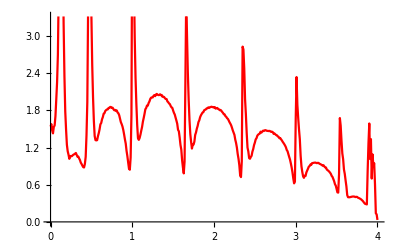

```mathematica
ListPlot[%17,Joined->True,PlotStyle->Red]
```

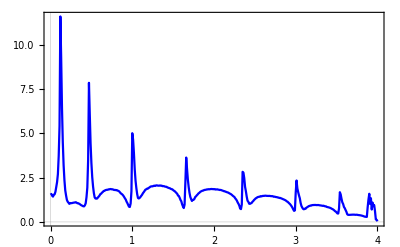

```mathematica
ListPlot[%17,PlotTheme->"Scientific",Joined->True,PlotStyle->Blue,PlotRange->All]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0,8],2]]},{ω,Range[0,4,0.01]}]
```

{{0.,7.99996},{0.01,7.99996},{0.02,7.99996},{0.03,7.99995},{0.04,7.99995},{0.05,7.99993},{0.06,7.99992},{0.07,7.99989},{0.08,7.99983},{0.09,7.99972},{0.1,7.9994},{0.11,7.99777},{0.12,7.76174},{0.13,7.00279},{0.14,7.00065},{0.15,7.00028},{0.16,7.00015},{0.17,7.00009},{0.18,7.00006},{0.19,7.00004},{0.2,7.00003},{0.21,7.00002},{0.22,7.00001},{0.23,7.00001},{0.24,7.00001},{0.25,7.},{0.26,7.},{0.27,7.},{0.28,7.},{0.29,7.},{0.3,6.99999},{0.31,6.99999},{0.32,6.99999},{0.33,6.99999},{0.34,6.99998},{0.35,6.99998},{0.36,6.99998},{0.37,6.99997},{0.38,6.99997},{0.39,6.99996},{0.4,6.99994},{0.41,6.99992},{0.42,6.99989},{0.43,6.99982},{0.44,6.99967},{0.45,6.99921},{0.46,6.99604},{0.47,6.04896},{0.48,6.00169},{0.49,6.0005},{0.5,6.00024},{0.51,6.00014},{0.52,6.00009},{0.53,6.00006},{0.54,6.00004},{0.55,6.00003},{0.56,6.00003},{0.57,6.00002},{0.58,6.00002},{0.59,6.00001},{0.6,6.00001},{0.61,6.00001},{0.62,6.00001},{0.63,6.00001},{0.64,6.},{0.65,6.},{0.66,6.},{0.67,6.},{0.68,6.},{0.69,6.},{0.7,6.},{0.71,6.},{0.72,6.},{0.73,6.},{0.74,6.},{0.75,6.},{0.76,6.},{0.77,6.},{0.78,5.99999},{0.79,5.99999},{0.8,5.99999},{0.81,5.99999},{0.82,5.99999},{0.83,5.99999},{0.84,5.99999},{0.85,5.99999},{0.86,5.99999},{0.87,5.99998},{0.88,5.99998},{0.89,5.99998},{0.9,5.99997},{0.91,5.99997},{0.92,5.99996},{0.93,5.99995},{0.94,5.99993},{0.95,5.9999},{0.96,5.99984},{0.97,5.99972},{0.98,5.99937},{0.99,5.9975},{1.,5.49987},{1.01,5.00247},{1.02,5.00062},{1.03,5.00027},{1.04,5.00015},{1.05,5.0001},{1.06,5.00007},{1.07,5.00005},{1.08,5.00004},{1.09,5.00003},{1.1,5.00002},{1.11,5.00002},{1.12,5.00001},{1.13,5.00001},{1.14,5.00001},{1.15,5.00001},{1.16,5.00001},{1.17,5.00001},{1.18,5.},{1.19,5.},{1.2,5.},{1.21,5.},{1.22,5.},{1.23,5.},{1.24,5.},{1.25,5.},{1.26,5.},{1.27,5.},{1.28,5.},{1.29,5.},{1.3,5.},{1.31,5.},{1.32,5.},{1.33,5.},{1.34,5.},{1.35,5.},{1.36,5.},{1.37,5.},{1.38,5.},{1.39,5.},{1.4,5.},{1.41,5.},{1.42,4.99999},{1.43,4.99999},{1.44,4.99999},{1.45,4.99999},{1.46,4.99999},{1.47,4.99999},{1.48,4.99999},{1.49,4.99999},{1.5,4.99999},{1.51,4.99999},{1.52,4.99998},{1.53,4.99998},{1.54,4.99998},{1.55,4.99997},{1.56,4.99997},{1.57,4.99996},{1.58,4.99995},{1.59,4.99993},{1.6,4.99991},{1.61,4.99986},{1.62,4.99976},{1.63,4.99951},{1.64,4.99845},{1.65,4.96891},{1.66,4.00461},{1.67,4.00083},{1.68,4.00033},{1.69,4.00018},{1.7,4.00011},{1.71,4.00007},{1.72,4.00005},{1.73,4.00004},{1.74,4.00003},{1.75,4.00002},{1.76,4.00002},{1.77,4.00002},{1.78,4.00001},{1.79,4.00001},{1.8,4.00001},{1.81,4.00001},{1.82,4.00001},{1.83,4.00001},{1.84,4.},{1.85,4.},{1.86,4.},{1.87,4.},{1.88,4.},{1.89,4.},{1.9,4.},{1.91,4.},{1.92,4.},{1.93,4.},{1.94,4.},{1.95,4.},{1.96,4.},{1.97,4.},{1.98,4.},{1.99,4.},{2.,4.},{2.01,4.},{2.02,4.},{2.03,4.},{2.04,4.},{2.05,4.},{2.06,4.},{2.07,4.},{2.08,4.},{2.09,4.},{2.1,4.},{2.11,4.},{2.12,3.99999},{2.13,3.99999},{2.14,3.99999},{2.15,3.99999},{2.16,3.99999},{2.17,3.99999},{2.18,3.99999},{2.19,3.99999},{2.2,3.99999},{2.21,3.99999},{2.22,3.99998},{2.23,3.99998},{2.24,3.99998},{2.25,3.99997},{2.26,3.99997},{2.27,3.99996},{2.28,3.99994},{2.29,3.99992},{2.3,3.99988},{2.31,3.99982},{2.32,3.99966},{2.33,3.99916},{2.34,3.99535},{2.35,3.03101},{2.36,3.00153},{2.37,3.00048},{2.38,3.00023},{2.39,3.00013},{2.4,3.00009},{2.41,3.00006},{2.42,3.00004},{2.43,3.00003},{2.44,3.00003},{2.45,3.00002},{2.46,3.00002},{2.47,3.00001},{2.48,3.00001},{2.49,3.00001},{2.5,3.00001},{2.51,3.00001},{2.52,3.00001},{2.53,3.},{2.54,3.},{2.55,3.},{2.56,3.},{2.57,3.},{2.58,3.},{2.59,3.},{2.6,3.},{2.61,3.},{2.62,3.},{2.63,3.},{2.64,3.},{2.65,3.},{2.66,3.},{2.67,3.},{2.68,3.},{2.69,3.},{2.7,3.},{2.71,3.},{2.72,3.},{2.73,3.},{2.74,3.},{2.75,3.},{2.76,3.},{2.77,2.99999},{2.78,2.99999},{2.79,2.99999},{2.8,2.99999},{2.81,2.99999},{2.82,2.99999},{2.83,2.99999},{2.84,2.99999},{2.85,2.99999},{2.86,2.99999},{2.87,2.99998},{2.88,2.99998},{2.89,2.99998},{2.9,2.99997},{2.91,2.99997},{2.92,2.99996},{2.93,2.99995},{2.94,2.99993},{2.95,2.9999},{2.96,2.99984},{2.97,2.99972},{2.98,2.99937},{2.99,2.99751},{3.,2.49987},{3.01,2.00247},{3.02,2.00062},{3.03,2.00027},{3.04,2.00015},{3.05,2.0001},{3.06,2.00007},{3.07,2.00005},{3.08,2.00004},{3.09,2.00003},{3.1,2.00002},{3.11,2.00002},{3.12,2.00001},{3.13,2.00001},{3.14,2.00001},{3.15,2.00001},{3.16,2.00001},{3.17,2.00001},{3.18,2.},{3.19,2.},{3.2,2.},{3.21,2.},{3.22,2.},{3.23,2.},{3.24,2.},{3.25,2.},{3.26,2.},{3.27,2.},{3.28,2.},{3.29,2.},{3.3,2.},{3.31,2.},{3.32,2.},{3.33,1.99999},{3.34,1.99999},{3.35,1.99999},{3.36,1.99999},{3.37,1.99999},{3.38,1.99999},{3.39,1.99999},{3.4,1.99998},{3.41,1.99998},{3.42,1.99998},{3.43,1.99997},{3.44,1.99997},{3.45,1.99996},{3.46,1.99995},{3.47,1.99993},{3.48,1.9999},{3.49,1.99985},{3.5,1.99975},{3.51,1.99948},{3.52,1.99829},{3.53,1.95093},{3.54,1.00393},{3.55,1.00077},{3.56,1.00031},{3.57,1.00017},{3.58,1.0001},{3.59,1.00007},{3.6,1.00005},{3.61,1.00004},{3.62,1.00003},{3.63,1.00002},{3.64,1.00002},{3.65,1.00001},{3.66,1.00001},{3.67,1.00001},{3.68,1.},{3.69,1.},{3.7,1.},{3.71,0.999998},{3.72,0.999996},{3.73,0.999994},{3.74,0.999992},{3.75,0.999989},{3.76,0.999986},{3.77,0.999982},{3.78,0.999977},{3.79,0.999971},{3.8,0.999962},{3.81,0.999949},{3.82,0.99993},{3.83,0.999898},{3.84,0.999838},{3.85,0.999709},{3.86,0.999332},{3.87,0.997175},{3.88,0.23804},{3.89,0.00219442},{3.9,0.000583082},{3.91,0.000264242},{3.92,0.000150124},{3.93,0.0000967214},{3.94,0.0000675257},{3.95,0.0000498471},{3.96,0.0000383377},{3.97,0.0000304276},{3.98,0.0000247574},{3.99,0.0000205539},{4.,0.0000173505}}

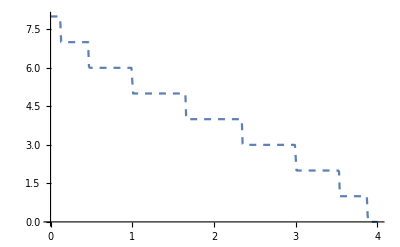

```mathematica
ListPlot[%19,Joined->True,PlotStyle->Dashed]
```

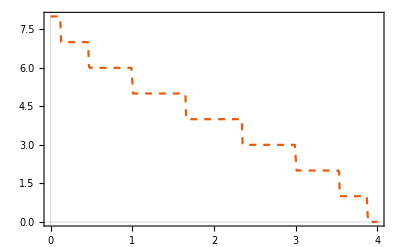

```mathematica
ListPlot[%19,PlotTheme->"Scientific",Joined->True,PlotStyle->Dashing[{Small,Small}]]
```

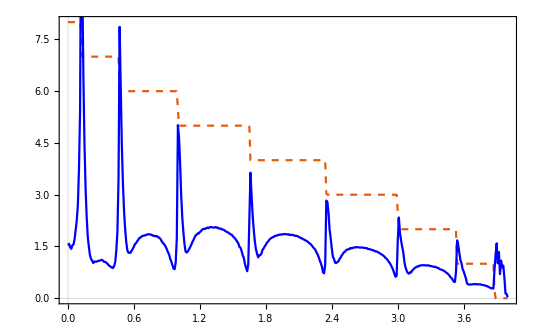

```mathematica
Show[%24,%29]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,9],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.03359},{0.01,1.8545},{0.02,1.80828},{0.03,1.75934},{0.04,1.97129},{0.05,2.07919},{0.06,2.49465},{0.07,3.14367},{0.08,4.11303},{0.09,6.47632},{0.1,13.127},{0.11,8.65647},{0.12,5.6541},{0.13,3.71233},{0.14,2.61211},{0.15,1.94393},{0.16,1.54873},{0.17,1.30694},{0.18,1.20402},{0.19,1.15893},{0.2,1.14132},{0.21,1.14927},{0.22,1.14079},{0.23,1.15068},{0.24,1.14757},{0.25,1.1257},{0.26,1.13177},{0.27,1.11856},{0.28,1.09795},{0.29,1.04923},{0.3,1.03829},{0.31,1.02918},{0.32,0.993981},{0.33,1.02597},{0.34,1.04372},{0.35,1.2524},{0.36,1.67527},{0.37,2.84032},{0.38,6.46968},{0.39,6.90218},{0.4,5.08059},{0.41,3.53002},{0.42,2.70102},{0.43,2.03449},{0.44,1.68364},{0.45,1.57764},{0.46,1.49247},{0.47,1.55763},{0.48,1.61936},{0.49,1.68487},{0.5,1.76915},{0.51,1.84713},{0.52,1.89235},{0.53,1.95496},{0.54,2.00717},{0.55,2.01488},{0.56,2.06343},{0.57,2.08889},{0.58,2.0846},{0.59,2.11314},{0.6,2.11213},{0.61,2.07502},{0.62,2.10513},{0.63,2.09505},{0.64,2.08105},{0.65,2.05746},{0.66,2.03502},{0.67,2.01446},{0.68,1.97534},{0.69,1.9378},{0.7,1.89361},{0.71,1.83416},{0.72,1.76431},{0.73,1.68488},{0.74,1.61665},{0.75,1.50489},{0.76,1.3778},{0.77,1.23579},{0.78,1.08956},{0.79,0.95988},{0.8,0.955301},{0.81,1.27271},{0.82,2.86257},{0.83,5.08909},{0.84,4.27668},{0.85,3.05999},{0.86,2.46174},{0.87,1.92407},{0.88,1.7446},{0.89,1.69346},{0.9,1.64519},{0.91,1.66992},{0.92,1.78288},{0.93,1.87958},{0.94,1.96783},{0.95,2.06643},{0.96,2.14237},{0.97,2.18904},{0.98,2.23663},{0.99,2.29904},{1.,2.32902},{1.01,2.35116},{1.02,2.37459},{1.03,2.40517},{1.04,2.41914},{1.05,2.43856},{1.06,2.43153},{1.07,2.43928},{1.08,2.46332},{1.09,2.44353},{1.1,2.44935},{1.11,2.44229},{1.12,2.42793},{1.13,2.43883},{1.14,2.4199},{1.15,2.41932},{1.16,2.41038},{1.17,2.38572},{1.18,2.3647},{1.19,2.33062},{1.2,2.334},{1.21,2.32745},{1.22,2.25668},{1.23,2.26118},{1.24,2.19954},{1.25,2.14429},{1.26,2.11786},{1.27,2.0546},{1.28,1.98111},{1.29,1.92894},{1.3,1.83816},{1.31,1.72393},{1.32,1.61616},{1.33,1.48103},{1.34,1.29142},{1.35,1.08787},{1.36,0.908256},{1.37,1.01233},{1.38,2.81439},{1.39,3.97077},{1.4,3.08493},{1.41,2.43183},{1.42,1.97645},{1.43,1.67739},{1.44,1.54795},{1.45,1.52878},{1.46,1.57537},{1.47,1.64109},{1.48,1.74578},{1.49,1.82742},{1.5,1.95245},{1.51,2.01812},{1.52,2.07232},{1.53,2.12441},{1.54,2.17741},{1.55,2.21031},{1.56,2.25718},{1.57,2.26651},{1.58,2.30367},{1.59,2.31266},{1.6,2.3262},{1.61,2.33767},{1.62,2.33171},{1.63,2.35172},{1.64,2.36475},{1.65,2.36683},{1.66,2.36582},{1.67,2.34738},{1.68,2.35796},{1.69,2.37395},{1.7,2.363},{1.71,2.33546},{1.72,2.34416},{1.73,2.32645},{1.74,2.32675},{1.75,2.30415},{1.76,2.31197},{1.77,2.29293},{1.78,2.28958},{1.79,2.27764},{1.8,2.25436},{1.81,2.24339},{1.82,2.20428},{1.83,2.1883},{1.84,2.15358},{1.85,2.13756},{1.86,2.12097},{1.87,2.06087},{1.88,2.03224},{1.89,1.98647},{1.9,1.93791},{1.91,1.87782},{1.92,1.81328},{1.93,1.73185},{1.94,1.65456},{1.95,1.53838},{1.96,1.38583},{1.97,1.18871},{1.98,1.01198},{1.99,0.953337},{2.,2.20509},{2.01,3.46636},{2.02,2.70113},{2.03,2.23455},{2.04,1.83111},{2.05,1.66637},{2.06,1.43194},{2.07,1.40304},{2.08,1.36489},{2.09,1.434},{2.1,1.49077},{2.11,1.54285},{2.12,1.634},{2.13,1.68229},{2.14,1.76081},{2.15,1.82061},{2.16,1.84222},{2.17,1.89214},{2.18,1.91437},{2.19,1.91274},{2.2,1.94928},{2.21,1.97704},{2.22,1.96696},{2.23,1.9951},{2.24,1.99653},{2.25,2.00762},{2.26,2.00508},{2.27,2.00521},{2.28,2.0058},{2.29,2.02198},{2.3,2.0113},{2.31,2.00617},{2.32,1.99623},{2.33,1.99946},{2.34,2.0033},{2.35,1.98503},{2.36,1.96643},{2.37,1.97123},{2.38,1.97106},{2.39,1.94665},{2.4,1.92251},{2.41,1.92127},{2.42,1.89748},{2.43,1.87858},{2.44,1.85419},{2.45,1.83808},{2.46,1.81977},{2.47,1.78308},{2.48,1.77603},{2.49,1.75007},{2.5,1.719},{2.51,1.67727},{2.52,1.63656},{2.53,1.5822},{2.54,1.5168},{2.55,1.4376},{2.56,1.35034},{2.57,1.25732},{2.58,1.12974},{2.59,0.979472},{2.6,0.79735},{2.61,0.827013},{2.62,2.50275},{2.63,2.43393},{2.64,2.04426},{2.65,1.69215},{2.66,1.47126},{2.67,1.33111},{2.68,1.16678},{2.69,1.06112},{2.7,1.06687},{2.71,1.15349},{2.72,1.18561},{2.73,1.24976},{2.74,1.31331},{2.75,1.3595},{2.76,1.42008},{2.77,1.45246},{2.78,1.47107},{2.79,1.49012},{2.8,1.50712},{2.81,1.52542},{2.82,1.53027},{2.83,1.52197},{2.84,1.53187},{2.85,1.52716},{2.86,1.54312},{2.87,1.53318},{2.88,1.54108},{2.89,1.54431},{2.9,1.53572},{2.91,1.53315},{2.92,1.51658},{2.93,1.5102},{2.94,1.52915},{2.95,1.50852},{2.96,1.48016},{2.97,1.47773},{2.98,1.45697},{2.99,1.44562},{3.,1.43616},{3.01,1.41139},{3.02,1.39199},{3.03,1.3805},{3.04,1.37488},{3.05,1.33821},{3.06,1.31078},{3.07,1.27423},{3.08,1.23852},{3.09,1.20884},{3.1,1.15641},{3.11,1.11859},{3.12,1.04291},{3.13,0.973197},{3.14,0.878464},{3.15,0.770988},{3.16,0.665442},{3.17,0.735813},{3.18,2.02032},{3.19,1.94556},{3.2,1.56175},{3.21,1.42103},{3.22,1.17976},{3.23,1.0185},{3.24,0.855605},{3.25,0.759195},{3.26,0.745656},{3.27,0.746632},{3.28,0.779888},{3.29,0.818849},{3.3,0.859677},{3.31,0.896868},{3.32,0.921314},{3.33,0.93672},{3.34,0.956122},{3.35,0.960492},{3.36,0.975919},{3.37,0.966736},{3.38,0.966779},{3.39,0.958666},{3.4,0.966745},{3.41,0.946338},{3.42,0.960303},{3.43,0.947441},{3.44,0.94205},{3.45,0.930802},{3.46,0.918217},{3.47,0.899094},{3.48,0.894551},{3.49,0.869755},{3.5,0.85903},{3.51,0.845335},{3.52,0.829701},{3.53,0.809456},{3.54,0.768424},{3.55,0.741589},{3.56,0.689894},{3.57,0.662184},{3.58,0.609103},{3.59,0.559861},{3.6,0.500483},{3.61,0.50262},{3.62,1.32699},{3.63,1.50056},{3.64,1.39117},{3.65,1.12167},{3.66,0.948319},{3.67,0.809933},{3.68,0.70664},{3.69,0.589342},{3.7,0.502761},{3.71,0.416347},{3.72,0.389927},{3.73,0.424994},{3.74,0.395331},{3.75,0.405738},{3.76,0.404653},{3.77,0.410807},{3.78,0.415039},{3.79,0.404875},{3.8,0.400436},{3.81,0.393366},{3.82,0.391843},{3.83,0.372038},{3.84,0.354546},{3.85,0.348662},{3.86,0.330149},{3.87,0.321627},{3.88,0.307221},{3.89,0.304009},{3.9,0.385366},{3.91,1.17391},{3.92,1.62754},{3.93,1.09666},{3.94,1.48447},{3.95,1.33523},{3.96,0.799611},{3.97,0.737514},{3.98,0.56172},{3.99,0.471186},{4.,0.123695}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,10],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.39988},{0.01,2.21788},{0.02,2.13878},{0.03,2.25871},{0.04,2.44828},{0.05,3.03852},{0.06,3.92838},{0.07,5.80995},{0.08,12.48},{0.09,10.2941},{0.1,6.29817},{0.11,3.9973},{0.12,2.7132},{0.13,1.93957},{0.14,1.57577},{0.15,1.37597},{0.16,1.28916},{0.17,1.22876},{0.18,1.23229},{0.19,1.2219},{0.2,1.21729},{0.21,1.24538},{0.22,1.18298},{0.23,1.16725},{0.24,1.13689},{0.25,1.11515},{0.26,1.05059},{0.27,1.08155},{0.28,1.1131},{0.29,1.40604},{0.3,1.97062},{0.31,3.87501},{0.32,9.07974},{0.33,6.19543},{0.34,3.86314},{0.35,2.88964},{0.36,2.15519},{0.37,1.79774},{0.38,1.70314},{0.39,1.69025},{0.4,1.793},{0.41,1.86971},{0.42,1.95372},{0.43,2.07062},{0.44,2.1318},{0.45,2.16596},{0.46,2.26184},{0.47,2.29678},{0.48,2.30051},{0.49,2.33013},{0.5,2.33563},{0.51,2.35258},{0.52,2.31441},{0.53,2.30813},{0.54,2.2996},{0.55,2.27398},{0.56,2.24988},{0.57,2.17984},{0.58,2.12932},{0.59,2.06569},{0.6,1.97088},{0.61,1.89043},{0.62,1.75749},{0.63,1.588},{0.64,1.42473},{0.65,1.25973},{0.66,1.08757},{0.67,1.09022},{0.68,1.69584},{0.69,5.75454},{0.7,4.97705},{0.71,3.47319},{0.72,2.62186},{0.73,2.09719},{0.74,1.8712},{0.75,1.85124},{0.76,1.92454},{0.77,2.04545},{0.78,2.16817},{0.79,2.2935},{0.8,2.37919},{0.81,2.46397},{0.82,2.55917},{0.83,2.59326},{0.84,2.65021},{0.85,2.72484},{0.86,2.73721},{0.87,2.759},{0.88,2.77795},{0.89,2.78999},{0.9,2.81947},{0.91,2.80336},{0.92,2.8062},{0.93,2.84007},{0.94,2.83894},{0.95,2.8231},{0.96,2.81764},{0.97,2.80732},{0.98,2.77603},{0.99,2.75747},{1.,2.72345},{1.01,2.72405},{1.02,2.66141},{1.03,2.62663},{1.04,2.58322},{1.05,2.52197},{1.06,2.49141},{1.07,2.39413},{1.08,2.32298},{1.09,2.22693},{1.1,2.1039},{1.11,1.94315},{1.12,1.80786},{1.13,1.55845},{1.14,1.28449},{1.15,1.01327},{1.16,1.24484},{1.17,4.76832},{1.18,3.87634},{1.19,2.91387},{1.2,2.27378},{1.21,1.85637},{1.22,1.78379},{1.23,1.79873},{1.24,1.92013},{1.25,2.05948},{1.26,2.21878},{1.27,2.3243},{1.28,2.41806},{1.29,2.52324},{1.3,2.57817},{1.31,2.62962},{1.32,2.6935},{1.33,2.7387},{1.34,2.74777},{1.35,2.74878},{1.36,2.80355},{1.37,2.8113},{1.38,2.81908},{1.39,2.81946},{1.4,2.84441},{1.41,2.84992},{1.42,2.8427},{1.43,2.84202},{1.44,2.84242},{1.45,2.83404},{1.46,2.83302},{1.47,2.83723},{1.48,2.81158},{1.49,2.80334},{1.5,2.78237},{1.51,2.78265},{1.52,2.76896},{1.53,2.74852},{1.54,2.70534},{1.55,2.68304},{1.56,2.66768},{1.57,2.63871},{1.58,2.5764},{1.59,2.54825},{1.6,2.48013},{1.61,2.45883},{1.62,2.39203},{1.63,2.31701},{1.64,2.21039},{1.65,2.11452},{1.66,2.00272},{1.67,1.84385},{1.68,1.63233},{1.69,1.35089},{1.7,1.02821},{1.71,1.26013},{1.72,3.45057},{1.73,2.69836},{1.74,2.1478},{1.75,1.89922},{1.76,1.6455},{1.77,1.58618},{1.78,1.65728},{1.79,1.76723},{1.8,1.88449},{1.81,2.01279},{1.82,2.14491},{1.83,2.23512},{1.84,2.2995},{1.85,2.35039},{1.86,2.40179},{1.87,2.43967},{1.88,2.47201},{1.89,2.49816},{1.9,2.50072},{1.91,2.50549},{1.92,2.52938},{1.93,2.53919},{1.94,2.54236},{1.95,2.54905},{1.96,2.56105},{1.97,2.57588},{1.98,2.551},{1.99,2.54777},{2.,2.53648},{2.01,2.54552},{2.02,2.53603},{2.03,2.53514},{2.04,2.51747},{2.05,2.51295},{2.06,2.49579},{2.07,2.48279},{2.08,2.46521},{2.09,2.43534},{2.1,2.4375},{2.11,2.42536},{2.12,2.3925},{2.13,2.36643},{2.14,2.32765},{2.15,2.29548},{2.16,2.26515},{2.17,2.22545},{2.18,2.18007},{2.19,2.11162},{2.2,2.05701},{2.21,1.99395},{2.22,1.90618},{2.23,1.80668},{2.24,1.6509},{2.25,1.47669},{2.26,1.23419},{2.27,0.943734},{2.28,1.10024},{2.29,2.83733},{2.3,2.42659},{2.31,1.98752},{2.32,1.71124},{2.33,1.49368},{2.34,1.40953},{2.35,1.41251},{2.36,1.49706},{2.37,1.57405},{2.38,1.70008},{2.39,1.78874},{2.4,1.86498},{2.41,1.92732},{2.42,1.97085},{2.43,2.01034},{2.44,2.05008},{2.45,2.05956},{2.46,2.08134},{2.47,2.10509},{2.48,2.12677},{2.49,2.12882},{2.5,2.13059},{2.51,2.13143},{2.52,2.14147},{2.53,2.13114},{2.54,2.13745},{2.55,2.1179},{2.56,2.11965},{2.57,2.11546},{2.58,2.11649},{2.59,2.09087},{2.6,2.09197},{2.61,2.06323},{2.62,2.07231},{2.63,2.05308},{2.64,2.02886},{2.65,2.02698},{2.66,1.99651},{2.67,1.98637},{2.68,1.96253},{2.69,1.93709},{2.7,1.91368},{2.71,1.8955},{2.72,1.84583},{2.73,1.81001},{2.74,1.75033},{2.75,1.70576},{2.76,1.67203},{2.77,1.57214},{2.78,1.49938},{2.79,1.3819},{2.8,1.23672},{2.81,1.02065},{2.82,0.801482},{2.83,1.5459},{2.84,2.34875},{2.85,1.98086},{2.86,1.58502},{2.87,1.43363},{2.88,1.25102},{2.89,1.15124},{2.9,1.15156},{2.91,1.18659},{2.92,1.22979},{2.93,1.30256},{2.94,1.37415},{2.95,1.43746},{2.96,1.47629},{2.97,1.5234},{2.98,1.54777},{2.99,1.56134},{3.,1.57071},{3.01,1.58666},{3.02,1.59199},{3.03,1.58182},{3.04,1.59086},{3.05,1.59253},{3.06,1.59306},{3.07,1.58524},{3.08,1.56703},{3.09,1.56001},{3.1,1.56207},{3.11,1.56286},{3.12,1.54742},{3.13,1.52796},{3.14,1.49741},{3.15,1.50833},{3.16,1.47308},{3.17,1.46633},{3.18,1.44283},{3.19,1.42448},{3.2,1.37944},{3.21,1.3625},{3.22,1.30712},{3.23,1.3007},{3.24,1.24479},{3.25,1.1936},{3.26,1.10679},{3.27,1.0244},{3.28,0.933048},{3.29,0.807854},{3.3,0.658153},{3.31,1.41317},{3.32,1.73057},{3.33,1.55552},{3.34,1.32853},{3.35,1.19915},{3.36,0.930622},{3.37,0.809464},{3.38,0.756701},{3.39,0.753929},{3.4,0.777511},{3.41,0.822487},{3.42,0.864033},{3.43,0.908043},{3.44,0.936605},{3.45,0.951288},{3.46,0.969935},{3.47,0.956148},{3.48,0.971563},{3.49,0.988712},{3.5,0.975108},{3.51,0.959573},{3.52,0.963808},{3.53,0.960961},{3.54,0.947623},{3.55,0.936749},{3.56,0.915615},{3.57,0.911356},{3.58,0.875815},{3.59,0.868759},{3.6,0.847171},{3.61,0.808724},{3.62,0.782253},{3.63,0.735793},{3.64,0.687182},{3.65,0.650432},{3.66,0.577998},{3.67,0.511521},{3.68,0.623631},{3.69,1.43028},{3.7,1.40731},{3.71,1.0979},{3.72,1.06132},{3.73,0.761618},{3.74,0.648021},{3.75,0.555417},{3.76,0.476359},{3.77,0.404734},{3.78,0.394454},{3.79,0.391974},{3.8,0.396115},{3.81,0.404336},{3.82,0.402017},{3.83,0.402765},{3.84,0.397512},{3.85,0.393326},{3.86,0.386553},{3.87,0.374111},{3.88,0.348301},{3.89,0.340639},{3.9,0.319974},{3.91,0.327593},{3.92,0.877008},{3.93,1.4329},{3.94,1.43172},{3.95,1.07971},{3.96,1.37236},{3.97,0.935405},{3.98,0.661608},{3.99,0.452009},{4.,0.543285}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,11],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,2.82407},{0.01,2.66867},{0.02,2.58947},{0.03,2.84194},{0.04,3.44697},{0.05,4.5953},{0.06,7.30997},{0.07,14.9921},{0.08,8.68226},{0.09,5.13479},{0.1,3.26737},{0.11,2.19745},{0.12,1.64211},{0.13,1.485},{0.14,1.32994},{0.15,1.35625},{0.16,1.28829},{0.17,1.28118},{0.18,1.286},{0.19,1.25275},{0.2,1.22162},{0.21,1.20022},{0.22,1.19543},{0.23,1.21481},{0.24,1.40864},{0.25,2.0147},{0.26,3.8565},{0.27,9.65163},{0.28,6.2193},{0.29,3.89208},{0.3,2.55401},{0.31,2.00355},{0.32,1.81116},{0.33,1.84167},{0.34,1.96196},{0.35,2.06289},{0.36,2.24088},{0.37,2.28931},{0.38,2.41256},{0.39,2.48015},{0.4,2.5228},{0.41,2.52735},{0.42,2.58593},{0.43,2.56205},{0.44,2.54918},{0.45,2.52896},{0.46,2.4929},{0.47,2.46051},{0.48,2.39489},{0.49,2.33345},{0.5,2.29129},{0.51,2.13948},{0.52,1.97245},{0.53,1.83901},{0.54,1.63828},{0.55,1.36824},{0.56,1.18371},{0.57,1.26141},{0.58,2.57278},{0.59,6.0551},{0.6,4.14439},{0.61,2.98208},{0.62,2.37087},{0.63,2.12984},{0.64,2.10893},{0.65,2.23549},{0.66,2.38876},{0.67,2.564},{0.68,2.68585},{0.69,2.82157},{0.7,2.93608},{0.71,3.0118},{0.72,3.03273},{0.73,3.08479},{0.74,3.12059},{0.75,3.1444},{0.76,3.17067},{0.77,3.17918},{0.78,3.17101},{0.79,3.18646},{0.8,3.1866},{0.81,3.18849},{0.82,3.17094},{0.83,3.15007},{0.84,3.14823},{0.85,3.10237},{0.86,3.09299},{0.87,3.05188},{0.88,2.9818},{0.89,2.90993},{0.9,2.86545},{0.91,2.76907},{0.92,2.69179},{0.93,2.57697},{0.94,2.41295},{0.95,2.20608},{0.96,1.94779},{0.97,1.62608},{0.98,1.27507},{0.99,1.19636},{1.,4.5267},{1.01,4.02809},{1.02,3.06597},{1.03,2.39878},{1.04,2.11382},{1.05,2.03762},{1.06,2.19441},{1.07,2.39809},{1.08,2.59764},{1.09,2.76352},{1.1,2.86982},{1.11,2.98041},{1.12,3.05144},{1.13,3.12488},{1.14,3.1569},{1.15,3.21669},{1.16,3.23538},{1.17,3.26411},{1.18,3.27169},{1.19,3.26943},{1.2,3.30961},{1.21,3.29916},{1.22,3.31038},{1.23,3.31693},{1.24,3.31576},{1.25,3.32835},{1.26,3.30143},{1.27,3.28272},{1.28,3.28925},{1.29,3.26052},{1.3,3.2522},{1.31,3.20987},{1.32,3.19188},{1.33,3.15983},{1.34,3.13643},{1.35,3.08867},{1.36,3.06121},{1.37,2.99497},{1.38,2.94039},{1.39,2.85562},{1.4,2.78529},{1.41,2.68056},{1.42,2.56133},{1.43,2.397},{1.44,2.21599},{1.45,1.95211},{1.46,1.55206},{1.47,1.10576},{1.48,2.03152},{1.49,3.42155},{1.5,2.7859},{1.51,2.18267},{1.52,1.96412},{1.53,1.91323},{1.54,2.04385},{1.55,2.22544},{1.56,2.37937},{1.57,2.55121},{1.58,2.68482},{1.59,2.79594},{1.6,2.87051},{1.61,2.92919},{1.62,2.95921},{1.63,3.01621},{1.64,3.04996},{1.65,3.07069},{1.66,3.08354},{1.67,3.09243},{1.68,3.10684},{1.69,3.12575},{1.7,3.1422},{1.71,3.1278},{1.72,3.12159},{1.73,3.10319},{1.74,3.12262},{1.75,3.11856},{1.76,3.10492},{1.77,3.10056},{1.78,3.08914},{1.79,3.08167},{1.8,3.06147},{1.81,3.03939},{1.82,3.02866},{1.83,2.99766},{1.84,2.96827},{1.85,2.94099},{1.86,2.91411},{1.87,2.90518},{1.88,2.83139},{1.89,2.80867},{1.9,2.76253},{1.91,2.7037},{1.92,2.61724},{1.93,2.54268},{1.94,2.45926},{1.95,2.31859},{1.96,2.15714},{1.97,1.94567},{1.98,1.61722},{1.99,1.20292},{2.,2.24329},{2.01,3.18471},{2.02,2.43614},{2.03,2.06838},{2.04,1.82123},{2.05,1.79799},{2.06,1.83153},{2.07,1.94059},{2.08,2.05764},{2.09,2.17266},{2.1,2.29007},{2.11,2.3939},{2.12,2.48122},{2.13,2.54511},{2.14,2.56772},{2.15,2.61318},{2.16,2.63925},{2.17,2.65136},{2.18,2.68474},{2.19,2.70874},{2.2,2.70225},{2.21,2.72172},{2.22,2.71112},{2.23,2.71551},{2.24,2.71963},{2.25,2.7191},{2.26,2.69983},{2.27,2.7048},{2.28,2.70704},{2.29,2.68308},{2.3,2.67203},{2.31,2.67188},{2.32,2.64422},{2.33,2.62971},{2.34,2.61078},{2.35,2.59052},{2.36,2.57114},{2.37,2.54528},{2.38,2.52766},{2.39,2.48765},{2.4,2.44534},{2.41,2.41712},{2.42,2.36432},{2.43,2.31529},{2.44,2.24073},{2.45,2.17535},{2.46,2.07614},{2.47,1.95508},{2.48,1.81794},{2.49,1.58316},{2.5,1.29074},{2.51,0.947107},{2.52,2.43607},{2.53,2.34102},{2.54,1.86071},{2.55,1.61139},{2.56,1.55583},{2.57,1.47746},{2.58,1.54852},{2.59,1.6142},{2.6,1.76508},{2.61,1.84768},{2.62,1.9408},{2.63,2.02964},{2.64,2.07852},{2.65,2.12316},{2.66,2.15895},{2.67,2.17046},{2.68,2.19146},{2.69,2.19534},{2.7,2.20562},{2.71,2.20986},{2.72,2.21267},{2.73,2.21447},{2.74,2.21814},{2.75,2.21459},{2.76,2.20929},{2.77,2.20242},{2.78,2.1922},{2.79,2.18325},{2.8,2.17952},{2.81,2.15251},{2.82,2.14888},{2.83,2.12219},{2.84,2.10384},{2.85,2.07968},{2.86,2.0607},{2.87,2.03829},{2.88,2.00071},{2.89,1.97248},{2.9,1.9384},{2.91,1.9043},{2.92,1.84879},{2.93,1.79011},{2.94,1.72457},{2.95,1.63224},{2.96,1.52413},{2.97,1.40468},{2.98,1.15803},{2.99,0.884514},{3.,1.64651},{3.01,1.91449},{3.02,1.65871},{3.03,1.44332},{3.04,1.2988},{3.05,1.1869},{3.06,1.14611},{3.07,1.1897},{3.08,1.25629},{3.09,1.35162},{3.1,1.44577},{3.11,1.50462},{3.12,1.53592},{3.13,1.57731},{3.14,1.59573},{3.15,1.60199},{3.16,1.60718},{3.17,1.62046},{3.18,1.62426},{3.19,1.62419},{3.2,1.62134},{3.21,1.60948},{3.22,1.61049},{3.23,1.61442},{3.24,1.59111},{3.25,1.57395},{3.26,1.56062},{3.27,1.55214},{3.28,1.52374},{3.29,1.49999},{3.3,1.47823},{3.31,1.45188},{3.32,1.4272},{3.33,1.38634},{3.34,1.33808},{3.35,1.30027},{3.36,1.24494},{3.37,1.16767},{3.38,1.07965},{3.39,0.961459},{3.4,0.796023},{3.41,0.718312},{3.42,1.6714},{3.43,1.51051},{3.44,1.29133},{3.45,1.12385},{3.46,0.8905},{3.47,0.798312},{3.48,0.753545},{3.49,0.785287},{3.5,0.815195},{3.51,0.871013},{3.52,0.903931},{3.53,0.943263},{3.54,0.947241},{3.55,0.972296},{3.56,0.976765},{3.57,0.979839},{3.58,0.983831},{3.59,0.965969},{3.6,0.965986},{3.61,0.960823},{3.62,0.940637},{3.63,0.91835},{3.64,0.899249},{3.65,0.865429},{3.66,0.845125},{3.67,0.828535},{3.68,0.788012},{3.69,0.736496},{3.7,0.685543},{3.71,0.611884},{3.72,0.536449},{3.73,0.625693},{3.74,1.35357},{3.75,1.22647},{3.76,0.997527},{3.77,0.92151},{3.78,0.726656},{3.79,0.518075},{3.8,0.499261},{3.81,0.455687},{3.82,0.440178},{3.83,0.404987},{3.84,0.410601},{3.85,0.39991},{3.86,0.39468},{3.87,0.391483},{3.88,0.387137},{3.89,0.371199},{3.9,0.350597},{3.91,0.343083},{3.92,0.322579},{3.93,0.463866},{3.94,1.73347},{3.95,1.08733},{3.96,1.0909},{3.97,0.815295},{3.98,0.742241},{3.99,0.437245},{4.,0.305493}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,12],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.15921},{0.01,3.18827},{0.02,3.08303},{0.03,3.53234},{0.04,4.87527},{0.05,7.47216},{0.06,15.803},{0.07,8.83365},{0.08,4.7539},{0.09,3.0579},{0.1,2.08644},{0.11,1.67429},{0.12,1.52629},{0.13,1.43256},{0.14,1.41142},{0.15,1.35278},{0.16,1.33089},{0.17,1.3133},{0.18,1.29096},{0.19,1.31771},{0.2,1.43406},{0.21,1.91106},{0.22,3.48206},{0.23,10.4926},{0.24,6.45086},{0.25,4.09247},{0.26,2.71866},{0.27,2.10818},{0.28,1.9522},{0.29,2.09788},{0.3,2.24643},{0.31,2.38211},{0.32,2.53327},{0.33,2.63294},{0.34,2.65261},{0.35,2.73017},{0.36,2.7532},{0.37,2.72225},{0.38,2.71662},{0.39,2.7258},{0.4,2.69735},{0.41,2.65892},{0.42,2.54851},{0.43,2.41576},{0.44,2.27358},{0.45,2.10452},{0.46,1.8343},{0.47,1.54029},{0.48,1.26233},{0.49,1.40045},{0.5,3.82468},{0.51,5.68297},{0.52,3.7507},{0.53,2.77467},{0.54,2.32171},{0.55,2.32501},{0.56,2.50725},{0.57,2.72245},{0.58,2.91889},{0.59,3.08351},{0.6,3.20638},{0.61,3.33281},{0.62,3.36438},{0.63,3.43492},{0.64,3.49486},{0.65,3.46802},{0.66,3.55282},{0.67,3.54603},{0.68,3.5428},{0.69,3.55362},{0.7,3.53723},{0.71,3.53425},{0.72,3.47356},{0.73,3.4727},{0.74,3.43774},{0.75,3.37834},{0.76,3.32302},{0.77,3.24794},{0.78,3.15956},{0.79,3.02132},{0.8,2.89026},{0.81,2.71509},{0.82,2.48665},{0.83,2.14947},{0.84,1.71896},{0.85,1.25561},{0.86,2.18815},{0.87,4.68454},{0.88,3.39009},{0.89,2.68757},{0.9,2.37766},{0.91,2.38298},{0.92,2.58363},{0.93,2.83531},{0.94,3.07302},{0.95,3.23939},{0.96,3.38838},{0.97,3.48194},{0.98,3.55013},{0.99,3.60454},{1.,3.67556},{1.01,3.70897},{1.02,3.73904},{1.03,3.75938},{1.04,3.77588},{1.05,3.78051},{1.06,3.79397},{1.07,3.76794},{1.08,3.77925},{1.09,3.7561},{1.1,3.73628},{1.11,3.74084},{1.12,3.73027},{1.13,3.69479},{1.14,3.65232},{1.15,3.63972},{1.16,3.59719},{1.17,3.54864},{1.18,3.50472},{1.19,3.4409},{1.2,3.34172},{1.21,3.27274},{1.22,3.13233},{1.23,3.01484},{1.24,2.85038},{1.25,2.62864},{1.26,2.32771},{1.27,1.78134},{1.28,1.2326},{1.29,2.92358},{1.3,3.40594},{1.31,2.64328},{1.32,2.27761},{1.33,2.22545},{1.34,2.32103},{1.35,2.58784},{1.36,2.82992},{1.37,3.05821},{1.38,3.21071},{1.39,3.31995},{1.4,3.39931},{1.41,3.46708},{1.42,3.5265},{1.43,3.56021},{1.44,3.57569},{1.45,3.63363},{1.46,3.64112},{1.47,3.6402},{1.48,3.6497},{1.49,3.66856},{1.5,3.66999},{1.51,3.6584},{1.52,3.66555},{1.53,3.67028},{1.54,3.66003},{1.55,3.63538},{1.56,3.62721},{1.57,3.60049},{1.58,3.61198},{1.59,3.56101},{1.6,3.53262},{1.61,3.50798},{1.62,3.46763},{1.63,3.43056},{1.64,3.39592},{1.65,3.35361},{1.66,3.28978},{1.67,3.21384},{1.68,3.13169},{1.69,3.03449},{1.7,2.90929},{1.71,2.79082},{1.72,2.57803},{1.73,2.29446},{1.74,1.88505},{1.75,1.22883},{1.76,3.1574},{1.77,2.53954},{1.78,2.27923},{1.79,2.02391},{1.8,2.05277},{1.81,2.15675},{1.82,2.35629},{1.83,2.6051},{1.84,2.76565},{1.85,2.918},{1.86,3.02026},{1.87,3.07819},{1.88,3.14746},{1.89,3.19397},{1.9,3.23331},{1.91,3.25122},{1.92,3.28386},{1.93,3.28306},{1.94,3.30089},{1.95,3.29581},{1.96,3.29788},{1.97,3.31007},{1.98,3.30471},{1.99,3.30767},{2.,3.29593},{2.01,3.28673},{2.02,3.28615},{2.03,3.27713},{2.04,3.25311},{2.05,3.24601},{2.06,3.23355},{2.07,3.20618},{2.08,3.17289},{2.09,3.15469},{2.1,3.12174},{2.11,3.09228},{2.12,3.04186},{2.13,3.00429},{2.14,2.97276},{2.15,2.89214},{2.16,2.83842},{2.17,2.76983},{2.18,2.65023},{2.19,2.53349},{2.2,2.39532},{2.21,2.17936},{2.22,1.85399},{2.23,1.31534},{2.24,1.69967},{2.25,2.48449},{2.26,2.19268},{2.27,1.91888},{2.28,1.80911},{2.29,1.87339},{2.3,1.99555},{2.31,2.14176},{2.32,2.32444},{2.33,2.48049},{2.34,2.56888},{2.35,2.64606},{2.36,2.70963},{2.37,2.74034},{2.38,2.79911},{2.39,2.79543},{2.4,2.81604},{2.41,2.83671},{2.42,2.8354},{2.43,2.84052},{2.44,2.83959},{2.45,2.85537},{2.46,2.83618},{2.47,2.84454},{2.48,2.83797},{2.49,2.8239},{2.5,2.81858},{2.51,2.80553},{2.52,2.79047},{2.53,2.76316},{2.54,2.74695},{2.55,2.72199},{2.56,2.7091},{2.57,2.68075},{2.58,2.64669},{2.59,2.61403},{2.6,2.58024},{2.61,2.54475},{2.62,2.47915},{2.63,2.45005},{2.64,2.36317},{2.65,2.29173},{2.66,2.20047},{2.67,2.03851},{2.68,1.86733},{2.69,1.5679},{2.7,1.12894},{2.71,2.11982},{2.72,2.16196},{2.73,1.81086},{2.74,1.68455},{2.75,1.54141},{2.76,1.5248},{2.77,1.66161},{2.78,1.77113},{2.79,1.90343},{2.8,2.02321},{2.81,2.10613},{2.82,2.144},{2.83,2.2087},{2.84,2.23075},{2.85,2.2487},{2.86,2.25503},{2.87,2.2837},{2.88,2.28093},{2.89,2.2824},{2.9,2.28596},{2.91,2.28653},{2.92,2.26484},{2.93,2.25285},{2.94,2.24983},{2.95,2.24513},{2.96,2.23374},{2.97,2.21799},{2.98,2.20733},{2.99,2.17126},{3.,2.16163},{3.01,2.13738},{3.02,2.10186},{3.03,2.06664},{3.04,2.03035},{3.05,2.0064},{3.06,1.92835},{3.07,1.89828},{3.08,1.81115},{3.09,1.73458},{3.1,1.60857},{3.11,1.45728},{3.12,1.18992},{3.13,0.858331},{3.14,1.96845},{3.15,1.77155},{3.16,1.45263},{3.17,1.27321},{3.18,1.17689},{3.19,1.17408},{3.2,1.22498},{3.21,1.33181},{3.22,1.41143},{3.23,1.49498},{3.24,1.51935},{3.25,1.57278},{3.26,1.6074},{3.27,1.63223},{3.28,1.62429},{3.29,1.63795},{3.3,1.64922},{3.31,1.63718},{3.32,1.62265},{3.33,1.62434},{3.34,1.61763},{3.35,1.59396},{3.36,1.60253},{3.37,1.56927},{3.38,1.55356},{3.39,1.52592},{3.4,1.49603},{3.41,1.47192},{3.42,1.42691},{3.43,1.38814},{3.44,1.3346},{3.45,1.2696},{3.46,1.21398},{3.47,1.09018},{3.48,0.925133},{3.49,0.704055},{3.5,1.52766},{3.51,1.39873},{3.52,1.29584},{3.53,1.04618},{3.54,0.877755},{3.55,0.79725},{3.56,0.796326},{3.57,0.804245},{3.58,0.859578},{3.59,0.89615},{3.6,0.936397},{3.61,0.97077},{3.62,0.96763},{3.63,0.978715},{3.64,0.977181},{3.65,0.983537},{3.66,0.96362},{3.67,0.954388},{3.68,0.940327},{3.69,0.910234},{3.7,0.892541},{3.71,0.864505},{3.72,0.821494},{3.73,0.771143},{3.74,0.72381},{3.75,0.653625},{3.76,0.551033},{3.77,0.722876},{3.78,1.2011},{3.79,1.06906},{3.8,0.900557},{3.81,0.833264},{3.82,0.620005},{3.83,0.522326},{3.84,0.424458},{3.85,0.415011},{3.86,0.406258},{3.87,0.420583},{3.88,0.403725},{3.89,0.393629},{3.9,0.382667},{3.91,0.371661},{3.92,0.351582},{3.93,0.345177},{3.94,0.435122},{3.95,1.3498},{3.96,1.23084},{3.97,0.972295},{3.98,0.985406},{3.99,0.662223},{4.,0.606846}}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.001,1,0,1,13],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,3.69664},{0.01,3.5065},{0.02,3.82102},{0.03,4.54506},{0.04,6.99747},{0.05,17.2315},{0.06,10.148},{0.07,5.19752},{0.08,3.04025},{0.09,2.15639},{0.1,1.68659},{0.11,1.57035},{0.12,1.48065},{0.13,1.42867},{0.14,1.39237},{0.15,1.38385},{0.16,1.38929},{0.17,1.52121},{0.18,1.9985},{0.19,3.93779},{0.2,10.5862},{0.21,5.9282},{0.22,3.52852},{0.23,2.56765},{0.24,2.16168},{0.25,2.21308},{0.26,2.39185},{0.27,2.56585},{0.28,2.69097},{0.29,2.81904},{0.3,2.90678},{0.31,2.9721},{0.32,2.99088},{0.33,2.94046},{0.34,2.90546},{0.35,2.84309},{0.36,2.75751},{0.37,2.65114},{0.38,2.46584},{0.39,2.24692},{0.4,1.91974},{0.41,1.55178},{0.42,1.34757},{0.43,2.47946},{0.44,7.12332},{0.45,4.42335},{0.46,2.8581},{0.47,2.54443},{0.48,2.50388},{0.49,2.8258},{0.5,3.10473},{0.51,3.27472},{0.52,3.49774},{0.53,3.60136},{0.54,3.73278},{0.55,3.7695},{0.56,3.86366},{0.57,3.8691},{0.58,3.87274},{0.59,3.90497},{0.6,3.90605},{0.61,3.86258},{0.62,3.87537},{0.63,3.83704},{0.64,3.77003},{0.65,3.73558},{0.66,3.66659},{0.67,3.59212},{0.68,3.43451},{0.69,3.33555},{0.7,3.05946},{0.71,2.88033},{0.72,2.50135},{0.73,2.00951},{0.74,1.42908},{0.75,2.58522},{0.76,4.4723},{0.77,3.25196},{0.78,2.68244},{0.79,2.54377},{0.8,2.84131},{0.81,3.11454},{0.82,3.39515},{0.83,3.62134},{0.84,3.78828},{0.85,3.91295},{0.86,4.01113},{0.87,4.07514},{0.88,4.14383},{0.89,4.15391},{0.9,4.19473},{0.91,4.2188},{0.92,4.23496},{0.93,4.22288},{0.94,4.25274},{0.95,4.24113},{0.96,4.21173},{0.97,4.18556},{0.98,4.17832},{0.99,4.13114},{1.,4.10412},{1.01,4.04509},{1.02,3.98458},{1.03,3.9446},{1.04,3.88058},{1.05,3.78987},{1.06,3.65338},{1.07,3.52512},{1.08,3.34037},{1.09,3.13837},{1.1,2.77286},{1.11,2.29006},{1.12,1.5818},{1.13,2.15122},{1.14,3.71441},{1.15,2.75781},{1.16,2.5192},{1.17,2.48635},{1.18,2.79021},{1.19,3.12001},{1.2,3.39897},{1.21,3.61296},{1.22,3.78209},{1.23,3.874},{1.24,3.98635},{1.25,4.0327},{1.26,4.09112},{1.27,4.11921},{1.28,4.15116},{1.29,4.17817},{1.3,4.17929},{1.31,4.19601},{1.32,4.19994},{1.33,4.189},{1.34,4.19851},{1.35,4.17524},{1.36,4.16967},{1.37,4.15478},{1.38,4.1407},{1.39,4.12356},{1.4,4.09229},{1.41,4.07394},{1.42,4.03111},{1.43,3.98388},{1.44,3.93866},{1.45,3.90888},{1.46,3.82727},{1.47,3.74544},{1.48,3.65448},{1.49,3.55149},{1.5,3.39745},{1.51,3.21187},{1.52,2.94919},{1.53,2.62478},{1.54,1.96835},{1.55,1.28777},{1.56,3.04922},{1.57,2.61504},{1.58,2.32488},{1.59,2.30724},{1.6,2.56369},{1.61,2.87348},{1.62,3.14145},{1.63,3.33045},{1.64,3.50529},{1.65,3.6055},{1.66,3.69442},{1.67,3.75379},{1.68,3.80564},{1.69,3.83845},{1.7,3.86129},{1.71,3.87931},{1.72,3.90392},{1.73,3.90479},{1.74,3.9287},{1.75,3.91051},{1.76,3.91353},{1.77,3.91832},{1.78,3.90435},{1.79,3.92059},{1.8,3.89101},{1.81,3.87898},{1.82,3.85345},{1.83,3.83236},{1.84,3.81416},{1.85,3.79091},{1.86,3.77404},{1.87,3.73848},{1.88,3.71556},{1.89,3.65088},{1.9,3.60445},{1.91,3.54129},{1.92,3.45468},{1.93,3.3703},{1.94,3.26939},{1.95,3.15798},{1.96,2.98901},{1.97,2.74452},{1.98,2.38766},{1.99,1.74034},{2.,2.2848},{2.01,2.75417},{2.02,2.38727},{2.03,2.25953},{2.04,2.22819},{2.05,2.36764},{2.06,2.57264},{2.07,2.7849},{2.08,2.95915},{2.09,3.10372},{2.1,3.19351},{2.11,3.28633},{2.12,3.3405},{2.13,3.3674},{2.14,3.39308},{2.15,3.42202},{2.16,3.43942},{2.17,3.45666},{2.18,3.46617},{2.19,3.46606},{2.2,3.46916},{2.21,3.46871},{2.22,3.46328},{2.23,3.44744},{2.24,3.44053},{2.25,3.42417},{2.26,3.41614},{2.27,3.39916},{2.28,3.37507},{2.29,3.35361},{2.3,3.32921},{2.31,3.30359},{2.32,3.26243},{2.33,3.21837},{2.34,3.18762},{2.35,3.12528},{2.36,3.08835},{2.37,2.99227},{2.38,2.92164},{2.39,2.81448},{2.4,2.68805},{2.41,2.5172},{2.42,2.24951},{2.43,1.85291},{2.44,1.17854},{2.45,2.41053},{2.46,2.13344},{2.47,1.93352},{2.48,1.8438},{2.49,1.92879},{2.5,2.09446},{2.51,2.28401},{2.52,2.49886},{2.53,2.64995},{2.54,2.71054},{2.55,2.78927},{2.56,2.82994},{2.57,2.87762},{2.58,2.9058},{2.59,2.91767},{2.6,2.92686},{2.61,2.93368},{2.62,2.946},{2.63,2.9357},{2.64,2.92791},{2.65,2.931},{2.66,2.91487},{2.67,2.91293},{2.68,2.89215},{2.69,2.88738},{2.7,2.87589},{2.71,2.85612},{2.72,2.83897},{2.73,2.80145},{2.74,2.76052},{2.75,2.74056},{2.76,2.70762},{2.77,2.66785},{2.78,2.63154},{2.79,2.55932},{2.8,2.49506},{2.81,2.41997},{2.82,2.32592},{2.83,2.19751},{2.84,1.99381},{2.85,1.7304},{2.86,1.20986},{2.87,1.98509},{2.88,1.99814},{2.89,1.80592},{2.9,1.55334},{2.91,1.54597},{2.92,1.64072},{2.93,1.80991},{2.94,1.95095},{2.95,2.08309},{2.96,2.15277},{2.97,2.21561},{2.98,2.23963},{2.99,2.29815},{3.,2.3035},{3.01,2.30814},{3.02,2.3176},{3.03,2.31863},{3.04,2.32248},{3.05,2.31401},{3.06,2.31609},{3.07,2.30446},{3.08,2.28679},{3.09,2.27431},{3.1,2.2633},{3.11,2.22928},{3.12,2.20946},{3.13,2.184},{3.14,2.16552},{3.15,2.12052},{3.16,2.10151},{3.17,2.03793},{3.18,1.97904},{3.19,1.92075},{3.2,1.84817},{3.21,1.75087},{3.22,1.59348},{3.23,1.36256},{3.24,0.975293},{3.25,1.8164},{3.26,1.64364},{3.27,1.43025},{3.28,1.23336},{3.29,1.19408},{3.3,1.19828},{3.31,1.28682},{3.32,1.37815},{3.33,1.49831},{3.34,1.54581},{3.35,1.59433},{3.36,1.63139},{3.37,1.63412},{3.38,1.64523},{3.39,1.6474},{3.4,1.64866},{3.41,1.63024},{3.42,1.63856},{3.43,1.62149},{3.44,1.60525},{3.45,1.57945},{3.46,1.56811},{3.47,1.53982},{3.48,1.51594},{3.49,1.47691},{3.5,1.44003},{3.51,1.37737},{3.52,1.32148},{3.53,1.22349},{3.54,1.10114},{3.55,0.922696},{3.56,0.686879},{3.57,1.44328},{3.58,1.3361},{3.59,1.11833},{3.6,0.97495},{3.61,0.827344},{3.62,0.818257},{3.63,0.82564},{3.64,0.860594},{3.65,0.918059},{3.66,0.942151},{3.67,0.963587},{3.68,0.974566},{3.69,0.987027},{3.7,0.967588},{3.71,0.958936},{3.72,0.94416},{3.73,0.919234},{3.74,0.90122},{3.75,0.869437},{3.76,0.82732},{3.77,0.755429},{3.78,0.692354},{3.79,0.581694},{3.8,0.570314},{3.81,1.30295},{3.82,1.06532},{3.83,0.841835},{3.84,0.780972},{3.85,0.601373},{3.86,0.475059},{3.87,0.443393},{3.88,0.411822},{3.89,0.399843},{3.9,0.40408},{3.91,0.402508},{3.92,0.380512},{3.93,0.361706},{3.94,0.360594},{3.95,0.748599},{3.96,1.7374},{3.97,1.29485},{3.98,1.00433},{3.99,1.00347},{4.,0.626512}}